# Mean p value

## load data

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 , 0.0028 ,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001, 0.00067 ,0.0005},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500,4500,9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
tg={{0.003430184515278148,0.002155828227332618},{0.0011179088576272092,0.000542496243679735},{0.000367,0.0000866}};;(*T at which tau_Alpha =1000 or 10000*)
```

## Mean p

```mathematica
shapesIndexList[filename_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD,edgeLists,box,allPoints,data,peris,areas},
data=Import[filename,"Data"];
If[data=!=$Failed,
allPoints={Partition[Normal[data[[3,1]]],2],Partition[Normal[data[[3,Length[data[[3]]]]]],2]};
box={data[[1,1,1]],data[[1,1,4]]};
Flatten[Table[copies=Table[allPoints[[i]],9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Select[Flatten[translatedCopies[[1]],1],-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
areas=AnnotationValue[{vm,2},MeshCellMeasure];
peris=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
peris/areas
,{i,Length[allPoints]}]],{}
]
];
```

```mathematica
perimetersList[filename_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD,edgeLists,box,allPoints,data,peris,areas},
data=Import[filename,"Data"];
If[data=!=$Failed,
allPoints={Partition[Normal[data[[3,1]]],2],Partition[Normal[data[[3,Length[data[[3]]]]]],2]};
box={data[[1,1,1]],data[[1,1,4]]};
Flatten[Table[copies=Table[allPoints[[i]],9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Select[Flatten[translatedCopies[[1]],1],-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
peris=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
peris
,{i,Length[allPoints]}]],{}
]
];
```

```mathematica
ps=Table[Table[Flatten[Table[shapesIndexList[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/glassyDynamics_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}]],{i,Length[records[[p]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
periemters=Table[Table[Flatten[Table[perimetersList[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/glassyDynamics_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}]],{i,Length[records[[p]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
vm=VoronoiMesh[RandomReal[{-64,64},{4096,2}]];
```

```mathematica
testperis=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}])
```

```mathematica
testarea=AnnotationValue[{vm,2},MeshCellMeasure]
```

```mathematica
Mean[testperis/testarea]
```

2.34381

```mathematica
Mean[ps[[1,1]]]
```

3.93539

```mathematica
p0s[[1]]
```

3.8

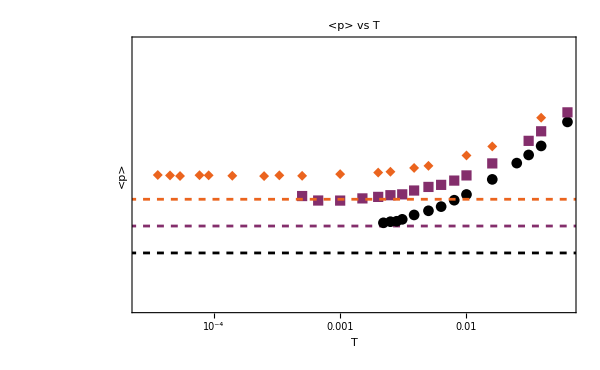

```mathematica
peimeter=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],Mean[periemters[[p,T]]]},{T,Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->Automatic,ImageSize->600,PlotStyle->gradientColScheme[5],(*PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}],*)PlotRange->{All,{3.75,4.0}},PlotLabel->"<p> vs T",FrameLabel->{"T","<p>"}],Table[LogLogPlot[p0s[[p]],{x,0.00001,0.1},PlotStyle->{gradientColScheme[5][[p]],Dashed}],{p,Length[p0s]}]]
```

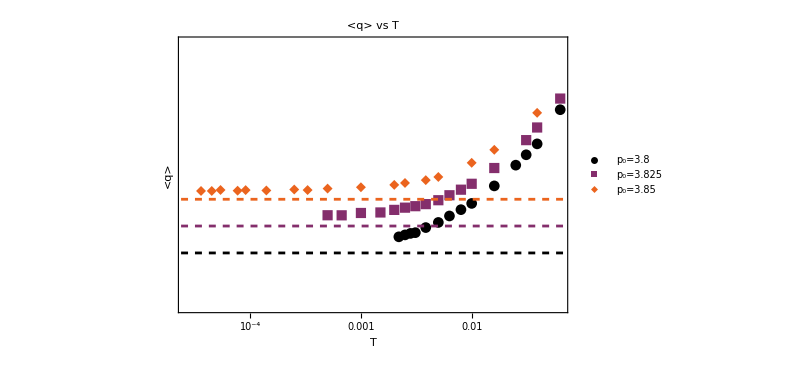

```mathematica
shape=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],Mean[ps[[p,T]]]},{T,Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->Automatic,ImageSize->600,PlotStyle->gradientColScheme[5],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}],PlotRange->{All,{3.75,4.0}},PlotLabel->"<q> vs T",FrameLabel->{"T","<q>"}],Table[LogLogPlot[p0s[[p]],{x,0.00001,0.1},PlotStyle->{gradientColScheme[5][[p]],Dashed}],{p,Length[p0s]}]]
```

```mathematica
Export["/home/chengling/Research/updates/07142024/shapeT.jpeg",Grid[Partition[{peimeter,shape},2]],ImageResolution->400]
```

/home/chengling/Research/updates/07142024/shapeT.jpeg

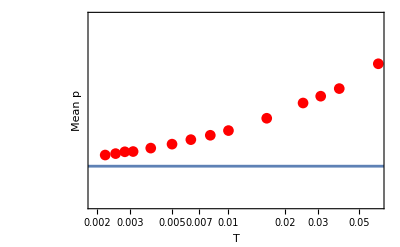
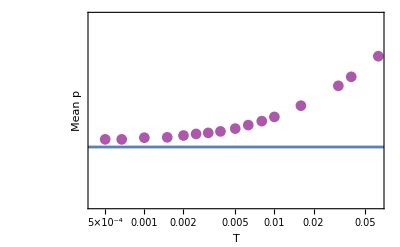
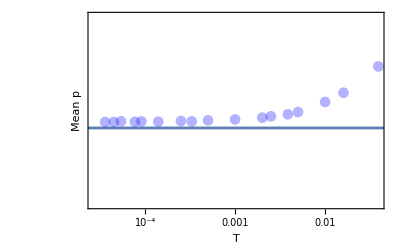

```mathematica
Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Mean[ps[[p,T]]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,ImageSize->400,PlotStyle->redBluePlotConfig[3][[p]],PlotRange->{All,{3.75,4.0}},FrameLabel->{"T","Mean p"}],LogLogPlot[p0s[[p]],{x,0.00001,0.1}]],{p,1,3}]
```